```mathematica
f[x_]=ⅇ^(x-x^2/4)*Tanh[x^3/11+1/3];
```

```mathematica
a= 0;
b=6;
n=6;
table= Table[{(a+b)/n *i ,f[(a+b)/n*i]},{i,0,n}]//N;
TableForm[table]
```

0. | 0.321513
1. | 0.847855
2. | 2.13629
3. | 2.10102
4. | 0.999991
5. | 0.286505
6. | 0.0497871

```mathematica
Fact[x_] =∏_(i=0)^n (x-(a+b)/n*i);
DifFactor[x_]=D[Fact[x],x];
Lagrang[x_]=Sum[f[(a+b)/n*i]*Fact[x]/((x-(a+b)/n*i)*DifFactor[(a+b)/n*i]),{i,0,n}]//N;
Expand[Lagrang[x]]
```

0.321513-1.13038 x+2.43962 x^2-0.827529 x^3+0.026763 x^4+0.0198283 x^5-0.00195986 x^6

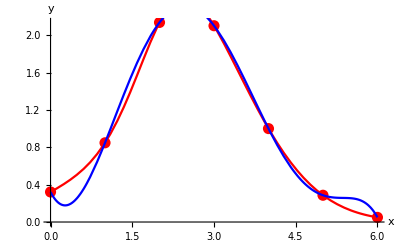

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[Lagrang[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
For[i=n,i≥ n-k,i--,
dif[i,k]=""
]
];
For[i=0,i≤n,i++,
dif[i,0]=table[[i+1,2]]
];
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]
]
];
tab=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tab],{5,2}]
```

0.32 |    0.53 |    0.76 |   -2.09 |    2.34 |   -1.15 |   -1.41
   0.85 |    1.29 |   -1.32 |    0.26 |    1.20 |   -2.56 | 
   2.14 |   -0.04 |   -1.07 |    1.45 |   -1.36 |  | 
   2.10 |   -1.10 |    0.39 |    0.09 |  |  | 
   1.00 |   -0.71 |    0.48 |  |  |  | 
   0.29 |   -0.24 |  |  |  |  | 
   0.05 |  |  |  |  |  |

```mathematica
h=(b-a)/n;
q=(x-b)/h;
NewT[x_]=dif[n,0];
qF[q_]=1;
For[i=1,i≤n,i++,
	qF[q_]=qF[q]*(q+i-1);
	NewT[q_]=NewT[q]+dif[n-i,i]/i!*qF[q];
]
NewT[x_]=Simplify[NewT[x]]
```

0.321513-1.13038 x+2.43962 x^2-0.827529 x^3+0.026763 x^4+0.0198283 x^5-0.00195986 x^6

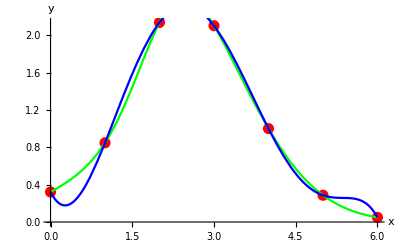

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Green],Plot[NewT[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

```mathematica
Np[x_]=InterpolatingPolynomial[table,x];
Np[x_]=Simplify[Np[x]]
```

0.321513-1.13038 x+2.43962 x^2-0.827529 x^3+0.026763 x^4+0.0198283 x^5-0.00195986 x^6

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[Np[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

-Graphics-

```mathematica
f[2.4316]
Lagrang[2.4316]
NewT[2.4316]
Np[2.4316]
```

2.40655

2.31605

2.31605

2.31605

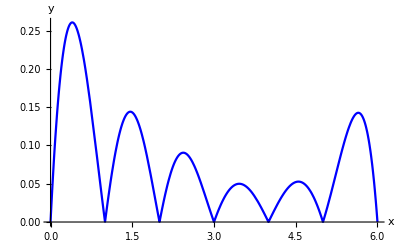

```mathematica
R[x_]=Abs[f[x]-Np[x]];
Plot[R[x],{x,0,6},PlotStyle->Blue,AxesLabel->{"x","y"}]
```

```mathematica
FindMaximum[{R[x],a<=x<=b}, x]
```

{0.260681,{x→0.398872}}

```mathematica
(*В случае для N=10*)
```

```mathematica
a= 0;
b=6;
n=10;
f[x_]=ⅇ^(x-x^2/4)*Tanh[x^3/11+1/3]
table= Table[{(a+b)/n *i ,f[(a+b)/n*i]},{i,0,n}]//N;
TableForm[table]
```

ⅇ^(x-x^2/4) Tanh[1/3+x^3/11]

0. | 0.321513
0.6 | 0.564545
1.2 | 1.05291
1.8 | 1.87865
2.4 | 2.40318
3. | 2.10102
3.6 | 1.43302
4.2 | 0.810583
4.8 | 0.382893
5.4 | 0.151072
6. | 0.0497871

```mathematica
Fact[x_] =∏_(i=0)^n (x-(a+b)/n*i);
DifFactor[x_]=D[Fact[x],x];
Lagrang[x_]=Sum[f[(a+b)/n*i]*Fact[x]/((x-(a+b)/n*i)*DifFactor[(a+b)/n*i]),{i,0,n}]//N;
Expand[Lagrang[x]]
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

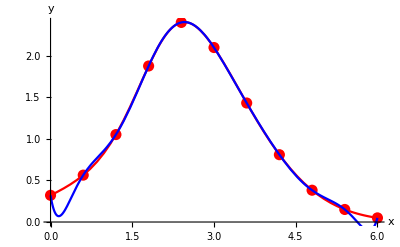

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[Lagrang[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
For[i=n,i≥ n-k,i--,
dif[i,k]=""
]
];
For[i=0,i≤n,i++,
dif[i,0]=table[[i+1,2]]
];
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]
]
];
tab=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tab],{5,2}]
```

0.32 |    0.24 |    0.25 |    0.09 |   -0.73 |    0.84 |    0.03 |   -1.94 |    4.67 |   -7.90 |   11.26
   0.56 |    0.49 |    0.34 |   -0.64 |    0.11 |    0.87 |   -1.91 |    2.73 |   -3.23 |    3.36 | 
   1.05 |    0.83 |   -0.30 |   -0.53 |    0.99 |   -1.04 |    0.82 |   -0.50 |    0.14 |  | 
   1.88 |    0.52 |   -0.83 |    0.46 |   -0.05 |   -0.21 |    0.33 |   -0.36 |  |  | 
   2.40 |   -0.30 |   -0.37 |    0.41 |   -0.26 |    0.11 |   -0.03 |  |  |  | 
   2.10 |   -0.67 |    0.05 |    0.15 |   -0.15 |    0.08 |  |  |  |  | 
   1.43 |   -0.62 |    0.19 |    0.00 |   -0.07 |  |  |  |  |  | 
   0.81 |   -0.43 |    0.20 |   -0.07 |  |  |  |  |  |  | 
   0.38 |   -0.23 |    0.13 |  |  |  |  |  |  |  | 
   0.15 |   -0.10 |  |  |  |  |  |  |  |  | 
   0.05 |  |  |  |  |  |  |  |  |  |

```mathematica
h=(b-a)/n;
q=(x-b)/h;
NewT[x_]=dif[n,0];
qF[q_]=1;
For[i=1,i≤n,i++,
	qF[q_]=qF[q]*(q+i-1);
	NewT[q_]=NewT[q]+dif[n-i,i]/i!*qF[q];
]
NewT[x_]=Simplify[NewT[x]]
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[NewT[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

-Graphics-

```mathematica
Np[x_]=InterpolatingPolynomial[table,x];
Np[x_]=Simplify[Np[x]]
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[Np[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

-Graphics-

```mathematica
f[2.4316]
Lagrang[2.4316]
NewT[2.4316]
Np[2.4316]
```

2.40655

2.4066

2.4066

2.4066

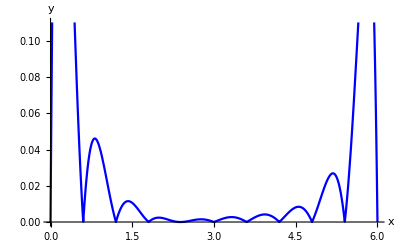

```mathematica
R[x_]=Abs[f[x]-Np[x]];
Plot[R[x],{x,0,6},PlotStyle->Blue,AxesLabel->{"x","y"}]
```

```mathematica
FindMaximum[{R[x],a<=x<=b}, x]
```

{0.0461276,{x→0.812717}}

```mathematica
f[x_]=ⅇ^(x-x^2/4)*Tanh[x^3/11+1/3];
```

```mathematica
сheb =Table[Cos[Pi*(2*i+1)/(2*n+2)],{i,0,n}];
Table2=Table[{Round[(a+b)/2+(b-a)/2*сheb[[n-i+1]], 10^-3]//N,Round[f[(a+b)/2+(b-a)/2*сheb[[n-i+1]]], 10^-3]//N},{i,0,n}];
TableForm[Table2]
```

0.031 | 0.331
0.271 | 0.416
0.733 | 0.643
1.378 | 1.274
2.155 | 2.287
3. | 2.101
3.845 | 1.16
4.622 | 0.487
5.267 | 0.188
5.729 | 0.084
5.969 | 0.053

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
For[i=n,i≥ n-k,i--,
dif[i,k]=""
]
];
For[i=0,i≤n,i++,
dif[i,0]=table[[i+1,2]]
];
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(table[[i+k+1,1]]-table[[i+1,1]])
]
];
tab=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tab],{5,2}]
```

0.32 |    0.41 |    0.34 |    0.07 |   -0.23 |    0.09 |    0.00 |   -0.01 |    0.01 |   -0.00 |    0.00
   0.56 |    0.81 |    0.47 |   -0.49 |    0.04 |    0.09 |   -0.06 |    0.02 |   -0.00 |    0.00 | 
   1.05 |    1.38 |   -0.42 |   -0.41 |    0.32 |   -0.11 |    0.02 |   -0.00 |    0.00 |  | 
   1.88 |    0.87 |   -1.15 |    0.36 |   -0.02 |   -0.02 |    0.01 |   -0.00 |  |  | 
   2.40 |   -0.50 |   -0.51 |    0.32 |   -0.08 |    0.01 |   -0.00 |  |  |  | 
   2.10 |   -1.11 |    0.06 |    0.12 |   -0.05 |    0.01 |  |  |  |  | 
   1.43 |   -1.04 |    0.27 |    0.00 |   -0.02 |  |  |  |  |  | 
   0.81 |   -0.71 |    0.27 |   -0.05 |  |  |  |  |  |  | 
   0.38 |   -0.39 |    0.18 |  |  |  |  |  |  |  | 
   0.15 |   -0.17 |  |  |  |  |  |  |  |  | 
   0.05 |  |  |  |  |  |  |  |  |  |

```mathematica
Pnr[x_]=dif[0,0];
p[x_]=1;
For[k=1,k≤n,k++,
p[x_]=p[x]*(x-table[[k,1]]);
Pnr[x_]=Pnr[x]+dif[0,k]*p[x];
]
Pnr[x_]=Simplify[Pnr[x]]
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

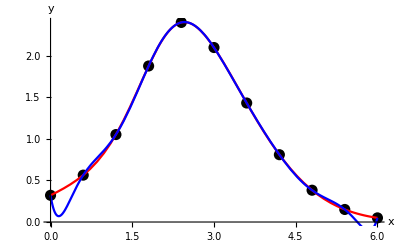

```mathematica
Show[ListPlot[table,PlotStyle->{ Black,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[Pnr[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

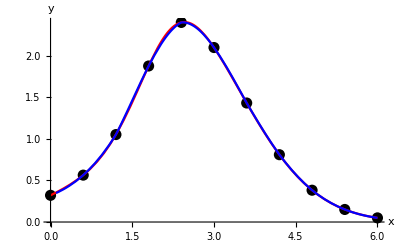

```mathematica
IntF=Interpolation[table];
Show[ListPlot[table,PlotStyle->{ Black,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[IntF[x],{x,0.1,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

```mathematica
f[2.4316]
Pnr[2.4316]
IntF[2.4316]
```

2.40655

2.4066

2.40385

```mathematica
R[x_]=Abs[f[x]-Pnr[x]];
```

```mathematica
FindMaximum[R[x],{x,0,6}]
```

{0.305839,{x→0.176716}}

```mathematica
R[x_]=Abs[f[x]-IntF[x]];
```

```mathematica
FindMaximum[R[x],{x,0,6}]
```

{0.00922482,{x→0.270776}}

```mathematica
a= 0;
b=6;
n=10;
сheb =Table[Cos[Pi*(2*i+1)/(2*n+2)],{i,0,n}];
Table2=Table[{Round[(a+b)/2+(b-a)/2*сheb[[n-i+1]], 10^-3]//N,Round[f[(a+b)/2+(b-a)/2*сheb[[n-i+1]]], 10^-3]//N},{i,0,n}];
TableForm[Table2]
```

0.031 | 0.331
0.271 | 0.416
0.733 | 0.643
1.378 | 1.274
2.155 | 2.287
3. | 2.101
3.845 | 1.16
4.622 | 0.487
5.267 | 0.188
5.729 | 0.084
5.969 | 0.053

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
For[i=n,i≥ n-k,i--,
dif[i,k]=""
]
];
For[i=0,i≤n,i++,
dif[i,0]=table[[i+1,2]]
];
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(table[[i+k+1,1]]-table[[i+1,1]])
]
];
tab=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[tab],{5,2}]
```

0.32 |    0.41 |    0.34 |    0.07 |   -0.23 |    0.09 |    0.00 |   -0.01 |    0.01 |   -0.00 |    0.00
   0.56 |    0.81 |    0.47 |   -0.49 |    0.04 |    0.09 |   -0.06 |    0.02 |   -0.00 |    0.00 | 
   1.05 |    1.38 |   -0.42 |   -0.41 |    0.32 |   -0.11 |    0.02 |   -0.00 |    0.00 |  | 
   1.88 |    0.87 |   -1.15 |    0.36 |   -0.02 |   -0.02 |    0.01 |   -0.00 |  |  | 
   2.40 |   -0.50 |   -0.51 |    0.32 |   -0.08 |    0.01 |   -0.00 |  |  |  | 
   2.10 |   -1.11 |    0.06 |    0.12 |   -0.05 |    0.01 |  |  |  |  | 
   1.43 |   -1.04 |    0.27 |    0.00 |   -0.02 |  |  |  |  |  | 
   0.81 |   -0.71 |    0.27 |   -0.05 |  |  |  |  |  |  | 
   0.38 |   -0.39 |    0.18 |  |  |  |  |  |  |  | 
   0.15 |   -0.17 |  |  |  |  |  |  |  |  | 
   0.05 |  |  |  |  |  |  |  |  |  |

```mathematica
Pnr[x_]=dif[0,0];
p[x_]=1;
For[k=1,k≤n,k++,
p[x_]=p[x]*(x-table[[k,1]]);
Pnr[x_]=Pnr[x]+dif[0,k]*p[x];
]
Pnr[x_]=Simplify[Pnr[x]]
```

0.321513-3.94488 x+19.9019 x^2-36.6729 x^3+36.1106 x^4-20.7358 x^5+7.29855 x^6-1.60185 x^7+0.214312 x^8-0.0160188 x^9+0.000513301 x^10

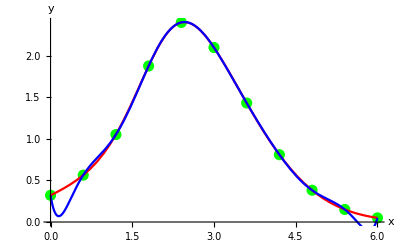

```mathematica
Show[ListPlot[table,PlotStyle->{ Green,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[Pnr[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

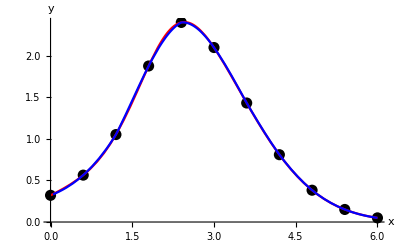

```mathematica
IntF=Interpolation[table];
Show[ListPlot[table,PlotStyle->{ Black,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],Plot[IntF[x],{x,0.045,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

```mathematica
f[2.4316]
Pnr[2.4316]
IntF[2.4316]
```

2.40655

2.4066

2.40385

```mathematica
R[x_]=Abs[f[x]-Pnr[x]];
```

```mathematica
FindMaximum[R[x],{x,0,6}]
```

{0.305839,{x→0.176716}}

```mathematica
R[x_]=Abs[f[x]-IntF[x]];
```

```mathematica
FindMaximum[R[x],{x,0,6}]
```

{0.00922482,{x→0.270776}}

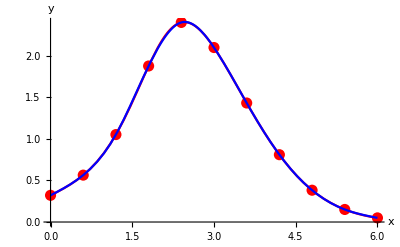

```mathematica
(*Задание 4*)
data={{0,0.3215},{0.6,0.5645},{1.2,1.0529},{1.8,1.8786},{2.4,2.4031},{3,2.1010},{3.6,1.4330},{4.2,0.8105},{4.8,0.3828},{5.4,0.1510},{6,0.0497}};
n=Length[data];
h=Table[data[[i+1,1]]-data[[i,1]],{i,n-1}];
a=Table[data[[i,2]],{i,n}];
alp=Table[3/h[[i]]*(a[[i+1]]-a[[i]])-3/h[[i-1]]*(a[[i]]-a[[i-1]]),{i,2,n-1}];
k1=Table[0,{i,n}];
k2=Table[0,{i,n}];
k3=Table[0,{i,n}];
k1[[1]]=1;k2[[1]]=0;k3[[1]]=0;
For[i=2,i<=n-1,i++,k1[[i]]=2*(data[[i+1,1]]-data[[i-1,1]])-h[[i-1]]*k2[[i-1]];
k2[[i]]=h[[i]]/k1[[i]];
k3[[i]]=(alp[[i-1]]-h[[i-1]]*k3[[i-1]])/k1[[i]];]
k1[[n]]=1;
k3[[n]]=0;
c=Table[0,{i,n}];
b=Table[0,{i,n-1}];
d=Table[0,{i,n-1}];
For[j=n-1,j>=1,j--,c[[j]]=k3[[j]]-k2[[j]]*c[[j+1]];
b[[j]]=(a[[j+1]]-a[[j]])/h[[j]]-h[[j]]*(c[[j+1]]+2*c[[j]])/3;
d[[j]]=(c[[j+1]]-c[[j]])/(3*h[[j]]);]

Spl[x_]:=Module[{j},j=1;
While[x>data[[j+1,1]],j++];
a[[j]]+b[[j]]*(x-data[[j,1]])+c[[j]]*(x-data[[j,1]])^2+d[[j]]*(x-data[[j,1]])^3]

Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},
PlotStyle->Red],Plot[Spl[x],{x,0,6},PlotStyle->Blue],AxesLabel->{"x","y"}]
```

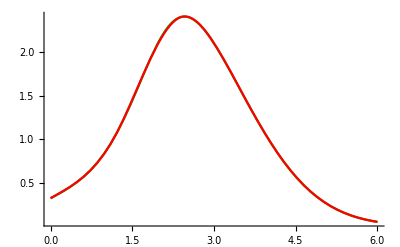

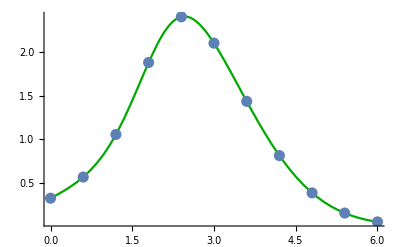

```mathematica
spl1= Interpolation[table, Method->"Spline"];
gr1 = Plot[f[x], {x, 0, 6}, PlotStyle->Darker[Green], PlotRange->All];
gr2 = ListPlot[data, PlotStyle->PointSize[0.02], PlotStyle->Blue, PlotRange->All];
gr3 = Plot[spl1[x],{x, 0, 6}, PlotStyle->Red, PlotRange->All];

Show[gr1, gr3]
Show[gr1,  gr2]
```

-Graphics-

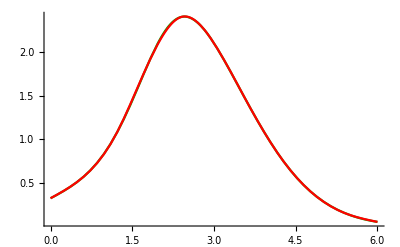

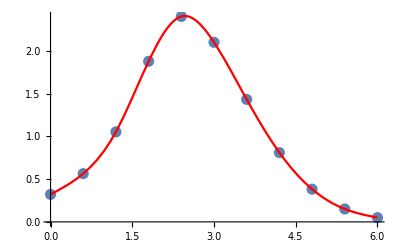

```mathematica
Needs["Splines`"]
spl2=SplineFit[data, Cubic];
gr4=ParametricPlot[spl2[x],{x,0,10},PlotStyle->Red,PlotStyle->Thickness[0.0015]];
Show[gr1, gr2]
Show[gr1,gr4]
Show[gr2, gr4]
```

```mathematica
f[x_]=ⅇ^(x-x^2/4)*Tanh[x^3/11+1/3];
Print[
{f[2.4316],
Spl[2.4316],
spl1[2.4316],
Round[Last[spl2[2.4316/0.6]],10^-3]// N
}
]
```

{2.40655,2.40741,2.40749,2.407}

{2.40655, 2.40658, 2.40749,2.407}

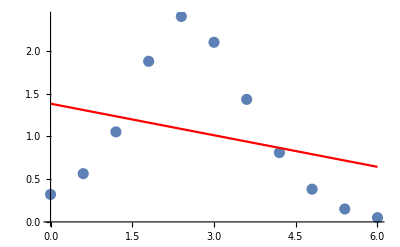

```mathematica
data={{0,0.3215},{0.6,0.5645},{1.2,1.0529},{1.8,1.8786},{2.4,2.4031},{3,2.1010},{3.6,1.4330},{4.2,0.8105},{4.8,0.3828},{5.4,0.1510},{6,0.0497}};

n=Length[data];
xValues=data[[All,1]];
yValues=data[[All,2]];
sumX=Total[xValues];
sumY=Total[yValues];
sumXY=Total[xValues*yValues];
sumX2=Total[xValues^2];
a1=(n*sumXY-sumX*sumY)/(n*sumX2-sumX^2);
a0=(sumY-a1*sumX)/n;
Q1[x_]:=a0+a1*x;


Show[ListPlot[data, PlotStyle->PointSize[0.02],PlotStyle->Blue],Plot[Q1[x],{x,0,6},PlotStyle->Red]]
```

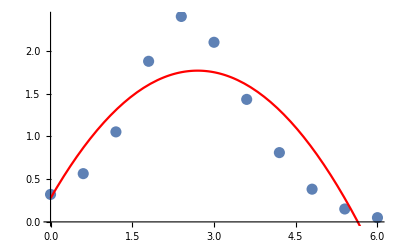

```mathematica
dataf = Table[{data[[i, 1]], f[data[[i, 1]]]}, {i, Length[data]}];


n = Length[data];
A = Table[{1, data[[i, 1]], data[[i, 1]]^2}, {i, n}];


B = Table[data[[i, 2]], {i, n}];


sol = LinearSolve[Transpose[A].A, Transpose[A].B];


Q2[x_] := sol[[1]] + sol[[2]] x + sol[[3]] x^2;

(* Строим график *)
Show[ListPlot[data, PlotStyle->PointSize[0.02],PlotStyle->Blue], Plot[Q2[x], {x, 0, 6}, PlotStyle->Red]]
```

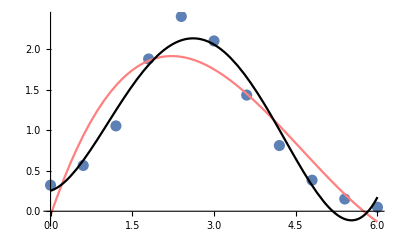

```mathematica
Clear[Q3]
Clear[Q4]
Q3[x_]=Fit[data,{1,x,x^2,x^3},x];
Q4[x_]=Fit[data,{1,x,x^2,x^3,x^4},x];
Show[ListPlot[data,PlotStyle->PointSize[0.02],PlotStyle->Blue],Plot[Q3[x],{x,0,6},PlotStyle->Pink],Plot[Q4[x],{x,0,6},PlotStyle->Black],PlotRange->All]
```

```mathematica
Print[{f[2.4316],Q1[2.4316], Q2[2.4316], Q3[2.4316], Q4[2.4316]}]
```

{2.40655,1.08352,1.75448,1.90135,2.11535}

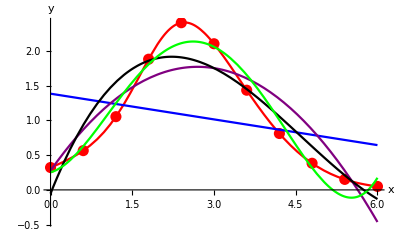

```mathematica
Show[ListPlot[table,PlotStyle->{ Red,PointSize[0.02]}],Plot[f[x],{x,0,6},PlotStyle->Red],
Plot[Q1[x],{x,0,6},PlotStyle->Blue],Plot[Q2[x],{x,0,6},PlotStyle->Purple],Plot[Q3[x],{x,0,6},PlotStyle->Black],Plot[Q4[x],{x,0,6},PlotStyle->Green],AxesLabel->{"x","y"}, PlotRange->All]
```